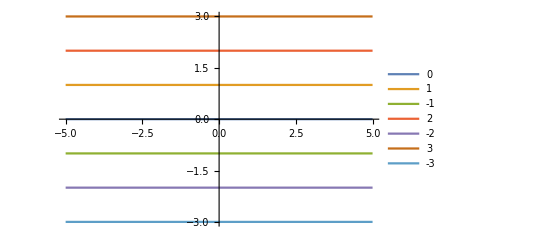

```mathematica
Plot[{0, 1, -1, 2, -2, 3, -3},{x,-5,5},PlotLegends->"Expressions"]
```

```mathematica
axes[x_,y_,z_,f_,a_]:=Graphics3D[Join[{Arrowheads[a]},Arrow[{{0,0,0},#}]&/@{{x,0,0},{0,y,0},{0,0,z}},{Text[Style["x",FontSize->Scaled[f]],{0.9*x,0.1*y,0.1*z}],Text[Style["y",FontSize->Scaled[f]],{0.1 x,0.9*y,0.1*z}],Text[Style["z",FontSize->Scaled[f]],{0.1*x,0.1*y,0.9*z}]}]]
```

```mathematica
Show[Plot3D[Abs[y],{x,-2,2},{y,-2,2},Boxed->False,PlotStyle->Opacity[0.7],Mesh->4,Axes->None],axes[2.5,2.5,1.5,0.05,0.02],PlotRange->{{-3,3},{-3,3},{0,1.5}}]
```

```mathematica
-Graphics3D-
Plot3D[Abs[y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

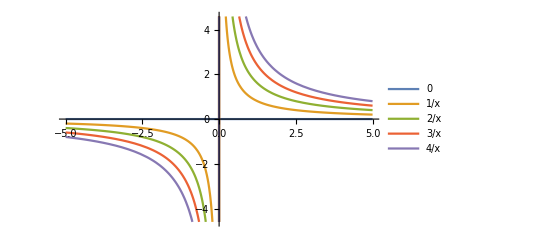

```mathematica
Plot[{0,1/x,2/x, 3/x, 4/x},{x,-5,5},PlotLegends->"Expressions"]
```

```mathematica
Show[Plot3D[x*y,{x,-2,2},{y,-2,2},Boxed->False,PlotStyle->Opacity[0.7],Mesh->4,Axes->None],axes[2.5,2.5,1.5,0.05,0.02],PlotRange->{{-3,3},{-3,3},{0,1.5}}]
```

-Graphics3D-

```mathematica
Plot3D[x*y,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x*y + z^2,{x,-3,3},{y,-3,3},{z,-3,3}]
```

-Graphics3D-

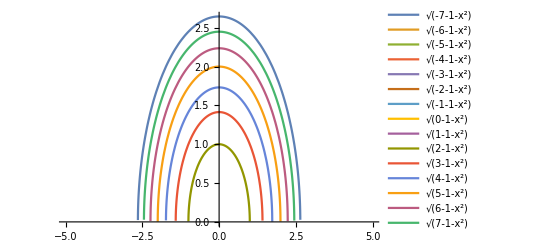

```mathematica
Plot[{Sqrt[-7 -1 -(x^2)], Sqrt[-6 -1 -(x^2)], Sqrt[-5 -1 -(x^2)], Sqrt[-4 -1 -(x^2)], Sqrt[-3 -1 -(x^2)], Sqrt[-2 -1 -(x^2)], Sqrt[-1 -1 -(x^2)], Sqrt[0 -1 -(x^2)], Sqrt[1 -1 -(x^2)], Sqrt[2 -1 -(x^2)], Sqrt[3 -1 -(x^2)], Sqrt[4 -1 -(x^2)], Sqrt[5 -1 -(x^2)], Sqrt[6 -1 -(x^2)], Sqrt[7 -1 -(x^2)], Sqrt[8-1 -(x^2)]},{x,-5,5},PlotLegends->"Expressions"]
```

```mathematica
Show[Plot3D[x^2 + y^2 + 1,{x,-2,2},{y,-2,2},Boxed->False,PlotStyle->Opacity[0.7],Mesh->4,Axes->None],axes[2.5,2.5,1.5,0.05,0.02],PlotRange->{{-3,3},{-3,3},{0,1.5}}]
```

-Graphics3D-

```mathematica
Plot3D[x^2 + y^2 + 1,{x,-2,2},{y,-2,2}]
```

-Graphics3D-